```mathematica
SetDirectory[NotebookDirectory[]];
<<rotationtools.wl
<<qtools.wl
```

# Dual Quaternion Control

```mathematica
(*Now define the FK of the interms of the six angles at each of the joint*)
```

```mathematica
(*Using the DH parameters of PUMA 560 robot*)
```

```mathematica
pq1 = unitdq[{0,0,0},θ1, {0,0,1}];
pq2 = unitdq[{0,0,0},-π/2, {1,0,0}];
pq3 = unitdq[{0,0,0},θ2, {0,0,1}];
pq4 =unitdq[{a2,0,0},0,{1,0,0}];
pq5 =unitdq[{0,0,d3},θ3,{0,0,1}];
pq6 = unitdq[{0, 0, 0}, -π/2, {1, 0, 0}];
pq7 = unitdq[{a3,0,0},0,{1,0,0}];
pq8 = unitdq[{0,0,d4},θ4,{0,0,1}];
pq9 = unitdq[{0,0,0},π/2,{1,0,0}];
pq10 = unitdq[{0,0,0},θ5,{0,0,1}];
pq11 = unitdq[{0,0,0},-π/2,{1,0,0}];
pq12 = unitdq[{0,0,0},θ6,{0,0,1}];
```

```mathematica
(*Now computing the fk quaternion*)
```

```mathematica
fkq = Simplify[dqmult[dqmult[dqmult[dqmult[dqmult[dqmult[dqmult[dqmult[dqmult[dqmult[dqmult[pq1, pq2], pq3], pq4], pq5], pq6], pq7], pq8], pq9], pq10], pq11], pq12]];
```

```mathematica
(*Validation of the FK*)
```

```mathematica
(*sampleangles3 = {θ1->3π/4, θ2->π/6, θ3->π/3, θ4->3π/4, θ5->-π/3, θ6->2π/3};*)
```

```mathematica
(*Produces great change*)
```

```mathematica
(*sampleangles3 = {θ1->3π/4, θ2->π/4, θ3->π/3, θ4->π/6, θ5->-π/4, θ6->2π/3};*)
```

```mathematica
(*Details of the PUMA 560 robot*)
```

```mathematica
params = {a2->0.4318 , d3->0.125, a3->0.019, d4->0.432};
sampleangles = {θ1->π/4, θ2->π/3, θ3->3π/4, θ4->π/6, θ5->-π/4, θ6->2π/3};
sampleangles2 = {θ1->π/2, θ2->π/6, θ3->π/3, θ4->3π/4, θ5->-π/3, θ6->2π/3};
sampleangles3 = {θ1->π/2, θ2->π/4, θ3->π/3, θ4->π/6, θ5->-π/4, θ6->2π/3};
```

```mathematica
fkqp= fkq/.params;
```

```mathematica
fkqs = N[fkq/.params/.sampleangles];
fkqs2 = N[fkq/.params/.sampleangles2];
fkqs3 = N[fkq/.params/.sampleangles3];
```

```mathematica
(*Finding the homogeneous transformation matrix from the dual quaternion*)
```

```mathematica
halfsin = Norm[fkqs[[1]][[2]]];
θs = 2*ArcTan[fkqs[[1]][[1]], Norm[fkqs[[1]][[2]]]];
kvecs = fkqs[[1]][[2]]/halfsin;
```

```mathematica
halfsin2 = Norm[fkqs2[[1]][[2]]];
θs2 = 2*ArcTan[fkqs2[[1]][[1]], Norm[fkqs2[[1]][[2]]]];
kvecs2 = fkqs2[[1]][[2]]/halfsin2;
```

```mathematica
Amats = vec2SkewMat[Tan[θs/2]*kvecs];
Amats2 = vec2SkewMat[Tan[θs2/2]*kvecs2];
```

```mathematica
(*Verifications with values given in Ghosal et. al.*)
```

```mathematica
Rmats = Inverse[IdentityMatrix[3]-Amats].(IdentityMatrix[3]+Amats)//MatrixForm
```

(0.974917 | -0.219152 | -0.0388486
0.164257 | 0.826234 | -0.538849
0.150188 | 0.518952 | 0.841506)

```mathematica
Rmats2 = Inverse[IdentityMatrix[3]-Amats2].(IdentityMatrix[3]+Amats2)//MatrixForm
```

(-0.789149 | 0.0473672 | 0.612372
-0.433013 | -0.75 | -0.5
0.435596 | -0.65974 | 0.612372)

```mathematica
tempt = {0, {tx, ty, tz}};
```

```mathematica
temptsol = Solve[((qmult[tempt, fkqs[[1]]] - 2*fkqs[[2]])[[2]])==0 ,{tx, ty, tz}][[1]]
```

{tx→0.13036,ty→0.307137,tz→0.0482477}

```mathematica
temptsol2 = Solve[((qmult[tempt, fkqs2[[1]]] - 2*fkqs2[[2]])[[2]])==0 ,{tx, ty, tz}][[1]]
```

{tx→-0.125,ty→-0.0580502,tz→-0.2349}

```mathematica
(*Residues*)
```

```mathematica
(qmult[tempt, fkqs[[1]]]-2*fkqs[[2]])/.temptsol
```

{5.89806×10^-17,{-6.93889×10^-18,5.55112×10^-17,1.38778×10^-17}}

```mathematica
(qmult[tempt, fkqs2[[1]]]-2*fkqs2[[2]])/.temptsol2
```

{-2.498×10^-16,{0.,1.38778×10^-17,6.93889×10^-18}}

```mathematica
(*Now we have an FK quaternion. We have to formulate the Jacobian in q terms. For which we flatten the quaternion and take the derivative wrt all the angles*)
```

```mathematica
flatfkq = Flatten[fkq];
```

```mathematica
(*Now computing the Jacobian, wrt θ*)
```

```mathematica
θsym = {θ1, θ2, θ3, θ4, θ5, θ6};
```

```mathematica
Jquatθ = D[flatfkq, {θsym}];
```

```mathematica
Jquatθs = N[Jquatθ/.params/.sampleangles];
```

```mathematica
(*Now we can proceed to do a kinematic control, assuming that the error is qe = qd-qc *)
```

```mathematica
(*Since the computation of pseudo inverse is tricky and expensive we keep it aside and go with J^T*)
```

```mathematica
(*Desired quaternion is*)
```

```mathematica
qd2 = N[fkq/.params/.sampleangles3];
```

```mathematica
qd = N[fkq/.params/.sampleangles2];
```

```mathematica
(*Initial quaternion is*)
```

```mathematica
qi = N[fkq/.params/.sampleangles];
```

```mathematica
(*Error dynamics is*)
```

```mathematica
Jqtp = Jquatθ/.params;
```

```mathematica
cJqtp = Compile[{{θ1, _Real}, {θ2, _Real}, {θ3, _Real}, {θ4, _Real}, {θ5, _Real},{θ6, _Real}}, Evaluate[Jqtp]];
```

```mathematica
cJqtps=cJqtp[(θsym/.sampleangles)[[1]], (θsym/.sampleangles)[[2]], (θsym/.sampleangles)[[3]], (θsym/.sampleangles)[[4]], (θsym/.sampleangles)[[5]], (θsym/.sampleangles)[[6]]]
```

{{0.0502218,-0.115485,-0.115485,0.069337,-0.132376,0.0502218},{-0.0247614,0.301879,0.301879,-0.120432,0.438329,0.0247614},{-0.138559,-0.372904,-0.372904,-0.21197,-0.195078,0.138559},{-0.477144,0.080467,0.080467,-0.430996,-0.0478354,-0.477144},{-0.0113817,0.0239944,0.0649279,0.050799,0.0025415,-0.0113817},{0.0733433,0.00349412,-0.141299,-0.0565544,-0.0112683,-0.0733433},{-0.0394101,0.012602,-0.130201,0.035835,-0.0066367,0.0394101},{0.00644026,0.0797287,0.019899,0.00635106,-0.0832222,0.00644026}}

```mathematica
Bmat[z_/;VectorQ[z, NumericQ]] := Module[{k, Bmattemp, Jqtpval, b2temp},
k = 185;
Jqtpval = cJqtp[z[[1]], z[[2]], z[[3]], z[[4]], z[[5]], z[[6]]];
Bmattemp = N[ArrayFlatten[{{ConstantArray[0,{14,6}],ArrayFlatten[{{Transpose[Jqtpval]*k}, {-Jqtpval.Transpose[Jqtpval]*k}}]}}]];
b2temp = Bmattemp.z;
Return[b2temp];
]
```

```mathematica
(*Initial error*)
```

```mathematica
qei = qd2-qi;
```

```mathematica
motionsim = NDSolve[{Bmat[z[t]]== z'[t],z[0]==Join[θsym/.sampleangles,Flatten[qei]]},z,{t, 0, 15}][[1]];
```

```mathematica
(*Final value reached vs desired value*)
```

```mathematica
thf = Flatten[z[t]/.motionsim/.t->15][[1;;6]]
thd = N[Flatten[θsym/.sampleangles3]]
```

{1.55914,0.791712,1.04536,0.533974,-0.794949,2.08381}

{1.5708,0.785398,1.0472,0.523599,-0.785398,2.0944}

```mathematica
(*Error in the quaternions*)
```

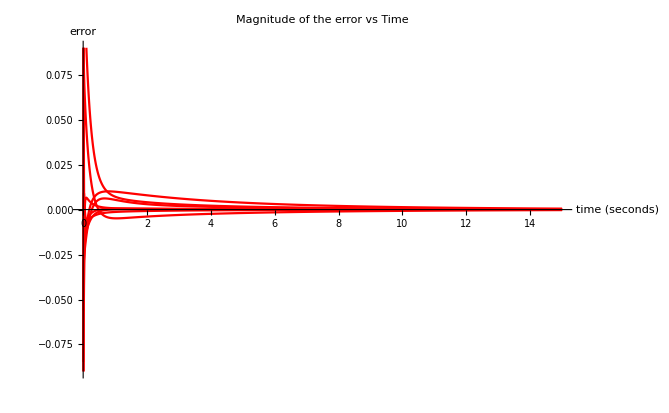

```mathematica
Plot[(z[t]/.motionsim)[[7;;14]], {t, 0, 15}, PlotStyle->Red, PlotRange->{{0,15},{-0.09,0.09}},AxesLabel->{"time (seconds) ", "error"}, PlotLabel->"Magnitude of the error vs Time"]
```

```mathematica
(z[t]/.motionsim/.t->10)[[7;;14]]
```

{0.000049824,0.0000613987,0.000103624,-0.000107632,0.00137179,-0.000705003,0.000569465,0.000487007}

```mathematica
(*Angles converging*)
```

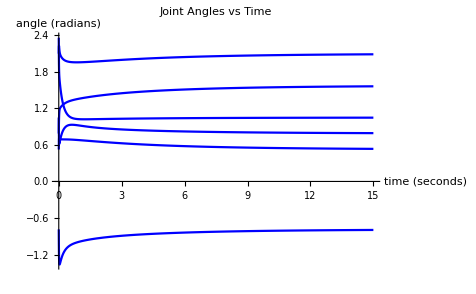

```mathematica
Plot[(z[t]/.motionsim)[[1;;6]], {t, 0, 15}, PlotStyle->Blue, AxesLabel-> {"time (seconds)", "angle (radians)"}, PlotLabel->"Joint Angles vs Time"]
```

```mathematica
(* Bringing the errors to within 2% *)
```

```mathematica
(Abs[thf-thd]/thd)*100
```

{0.741876,0.803963,0.175921,1.98154,-1.21604,0.505498}

```mathematica
(*Peak overshoot among all the other peaks*)
```

```mathematica
(*Table[Max[Table[(z[t]/.motionsim/.t->tval)[[j]]-thd[[j]],{tval, 0, 10, 0.01}]],{j, 6}]*)
```

```mathematica
(*Max steady state error*)
```

```mathematica
Max[Abs[thf-thd]]
```

0.0116534

```mathematica
(*Plotting the translation of the end-effector*)
```

```mathematica
zang = Table[(z[t]/.motionsim/.t->tval)[[1;;6]],{tval, 0, 15, 0.01}];
```

```mathematica
zθrule = Table[Inner[Rule, θsym, zang[[i]], List],{i,Dimensions[zang][[1]]}];
```

```mathematica
zlog = Table[2*(logdq[fkqp/.zθrule[[i]]]), {i, Dimensions[zang][[1]]}];
```

```mathematica
zdist = zlog[[;;,2]];
zang = zlog[[;;,1]];
```

```mathematica
ListPointPlot3D[zdist, PlotLabel->"Path followed by diffc", AxesLabel->{"x", "y", "z"}, PlotRange->{{-0.2, 0}, {-0.2, 0.2}, {-0.3, 0.3}}]
```

-Graphics3D-

```mathematica
(*We observe the discontinuities in the angles at the beginning*)
```

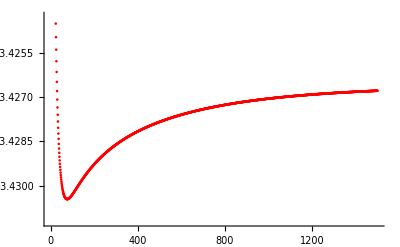

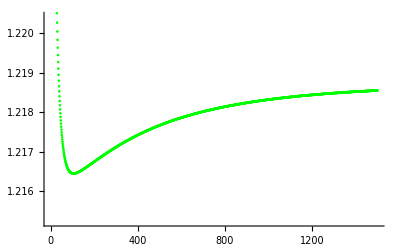

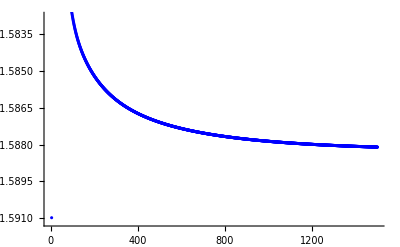

```mathematica
ListPlot[zang[[;;,1]], PlotStyle->{Red}]
ListPlot[zang[[;;,2]], PlotStyle->{Green}]
ListPlot[zang[[;;,3]], PlotStyle->{Blue}]
```

### Manipulate with a missing element

```mathematica
Manipulate[Show[frameplotter[Flatten[zlog[[1]]]], frameplotter[Flatten[zlog[[-1]]]], frameplotter[Flatten[zlog[[i]]]]],{i, 1, 500, 1}];
```

```mathematica
(*Increasing the resolution at the beginning*)
```

```mathematica
zangres = Table[(z[t]/.motionsim/.t->tval)[[1;;6]],{tval, 0, 1, 0.0001}];
```

```mathematica
zθruleres = Table[Inner[Rule, θsym, zangres[[i]], List],{i,Dimensions[zangres][[1]]}];
```

```mathematica
zlogres = Table[2*(logdq[fkqp/.zθruleres[[i]]]), {i, Dimensions[zangres][[1]]}];
```

### The missing element!

```mathematica
Manipulate[Show[frameplotter[Flatten[zlogres[[1]]]], frameplotter[Flatten[zlogres[[600]]]], frameplotter[Flatten[zlogres[[i]]]]],{i, 1, 600, 1}];
```

## Running the simulation for a lower gain value

```mathematica
Bmat[z_/;VectorQ[z, NumericQ]] := Module[{k, Bmattemp, Jqtpval, b2temp},
k = 10;
Jqtpval = cJqtp[z[[1]], z[[2]], z[[3]], z[[4]], z[[5]], z[[6]]];
Bmattemp = N[ArrayFlatten[{{ConstantArray[0,{14,6}],ArrayFlatten[{{Transpose[Jqtpval]*k}, {-Jqtpval.Transpose[Jqtpval]*k}}]}}]];
b2temp = Bmattemp.z;
Return[b2temp];
]
```

```mathematica
motionsimlow = NDSolve[{Bmat[z[t]]== z'[t],z[0]==Join[θsym/.sampleangles,Flatten[qei]]},z,{t, 0, 15}][[1]];
```

```mathematica
(*Plotting the translation of the end-effector*)
```

```mathematica
zanglow = Table[(z[t]/.motionsimlow/.t->tval)[[1;;6]],{tval, 0, 15, 0.005}];
```

```mathematica
zθrulelow = Table[Inner[Rule, θsym, zanglow[[i]], List],{i,1501}];
```

```mathematica
zloglow = Table[2*(logdq[fkqp/.zθrulelow[[i]]]), {i, 1501}];
```

```mathematica
zdistlow = zloglow[[;;,2]];
zanglow = zloglow[[;;,1]];
```

```mathematica
ListPointPlot3D[zdistlow, PlotLabel->"Path followed by diffc", AxesLabel->{"x", "y", "z"}, PlotRange->{{-0.2, 0}, {-0.2, 0.2}, {-0.3, 0.3}}]
```

-Graphics3D-

### Lower gain manipulate

```mathematica
Manipulate[Show[frameplotter[Flatten[zloglow[[1]]]], frameplotter[Flatten[zloglow[[-1]]]], frameplotter[Flatten[zloglow[[i]]]]],{i, 1, Dimensions[zloglow][[1]], 1}];
```

## Cooperative task-space control with two PUMA 560's

```mathematica
(*Primitive-1: Relative dual position control, so the controlled variable is qr. So we need the Jacbian for this control*)
```

```mathematica
(*We need fk of two robots in the cooperative workspace*)
```

```mathematica
αsym = {θ1, θ2, θ3, θ4, θ5, θ6}/.{θ1->α1, θ2->α2, θ3->α3, θ4->α4, θ5->α5, θ6->α6};
βsym = {θ1, θ2, θ3, θ4, θ5, θ6}/.{θ1->β1, θ2->β2, θ3->β3, θ4->β4, θ5->β5, θ6->β6};
```

```mathematica
fkq1 = fkq/.{θ1->α1, θ2->α2, θ3->α3, θ4->α4, θ5->α5, θ6->α6}/.params;
fkq2 = fkq/.{θ1->β1, θ2->β2, θ3->β3, θ4->β4, θ5->β5, θ6->β6}/.params;
```

```mathematica
Jq1 = D[Flatten[fkq1], {αsym}];
```

```mathematica
cq2 = cdualq[fkq2];
```

```mathematica
Jcq2 = D[Flatten[cq2], {βsym}];
```

```mathematica
sampleα = sampleangles/.{θ1->α1, θ2->α2, θ3->α3, θ4->α4, θ5->α5, θ6->α6};
sampleβ = sampleangles3/.{θ1->β1, θ2->β2, θ3->β3, θ4->β4, θ5->β5, θ6->β6};
```

```mathematica
Jqr = ArrayFlatten[{{dHn[fkq1].Jcq2, dHp[cq2].Jq1}}];
```

```mathematica
Jqr/.sampleα/.sampleβ//MatrixForm
```

(-0.135299 | 0.326641 | 0.326641 | -0.165707 | 0.330715 | -0.174071 | 0.135299 | -0.326641 | -0.326641 | 0.165707 | -0.330715 | 0.174071
-0.234616 | 0.275904 | 0.275904 | 0.0711268 | 0.369915 | 0.113159 | 0.234616 | -0.0985726 | -0.0985726 | 0.302097 | -0.195844 | 0.113159
-0.409741 | -0.253586 | -0.253586 | -0.0377388 | -0.0125703 | 0.316544 | 0.409741 | 0.229319 | 0.229319 | 0.362313 | 0.31407 | 0.316544
-0.0936042 | -0.0536388 | -0.0536388 | -0.46482 | -0.0602736 | -0.326641 | 0.0936042 | -0.284609 | -0.284609 | -0.00288066 | -0.0602736 | 0.326641
0.07392 | -0.039903 | -0.039903 | -0.009151 | -0.0640425 | -0.0913767 | -0.07392 | -0.039903 | 0.039903 | 0.009151 | 0.0640425 | 0.0913767
-0.0152876 | 0.0739037 | -0.0394088 | 0.0705204 | 0.0722049 | 0.0359057 | 0.0152876 | -0.0212107 | 0.138492 | 0.0921711 | 0.0191718 | 0.0359057
-0.00959682 | 0.0303179 | -0.116381 | -0.118005 | 0.0638252 | -0.09468 | 0.00959682 | -0.0245081 | 0.0156011 | -0.0805054 | 0.0944439 | -0.09468
-0.02652 | -0.00618699 | 0.104504 | 0.0236342 | 0.0784353 | -0.0306187 | 0.02652 | 0.0333952 | -0.0811916 | 0.0669355 | 0.0784353 | 0.0306187)

```mathematica
(*Primitive-2: Relative cartesian position control, so the controlled variable is tr. So we need the Jacbian for this control*)
```

```mathematica
dqr = dqmult[cdualq[fkq2], fkq1];
```

```mathematica
qr = dqr[[1]];
qr0 = dqr[[2]];
```

```mathematica
fullspace = Join[βsym, αsym];
```

```mathematica
Jqr0 = D[Flatten[qr0],{fullspace}];
```

```mathematica
Jcqr = D[Flatten[cquat[qr]],{fullspace}];
```

```mathematica
(*Gives the translation quaternion*)
```

```mathematica
Jtr = 2*(Hn[cquat[qr]].Jqr0+Hp[qr0].Jcqr);
```

```mathematica
Chop[Jtr/.sampleα/.sampleβ]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0.195637 | 0.25465 | 0.0545594 | 0.0181697 | 0.186389 | -0.297139 | -0.195637 | -0.23476 | 0.0510111 | 0 | 0 | 0
-0.159385 | 0.156883 | 0.184265 | -0.338433 | 0.322834 | -0.292229 | 0.159385 | -0.175722 | -0.415725 | 0 | 0 | 0
0.218288 | -0.0848627 | 0.296798 | 0.284007 | -0.111215 | 0 | -0.218288 | 0.109723 | -0.107496 | 0 | 0 | 0)

```mathematica
(*Now we have both the primitives required for pouring water into a glass. All we need is the required initial and final configurations*)
```

```mathematica
(*We have already assumed that both the arms start from the same point. This is an ok assumption as we are dealing with robots with two arms, hypotheticall originating from the same point in the body. Also we are dealing with virtual robots and hence collisions are ignored.*)
```

```mathematica
(*For the task of pouring water into a glass, we have the initial configuration, we need to decide on a final configuration to achieve this*)
```

```mathematica
(*Finding the initial relative distance between the two configurations*)
```

```mathematica
dqrs = N[dqr/.sampleα/.sampleβ]
```

{{0.653281,{-0.633088,0.226318,-0.348142}},{0.0612374,{0.18936,0.0718114,-0.182753}}}

```mathematica
qtrsi = 2*qmult[dqrs[[2]], cquat[dqrs[[1]]]]
```

{6.93889×10^-17,{0.292229,-0.297139,-0.372777}}

```mathematica
cJtr = Compile[{{β1, _Real}, {β2, _Real}, {β3, _Real}, {β4, _Real}, {β5, _Real},{β6, _Real}, {α1, _Real}, {α2, _Real}, {α3, _Real}, {α4, _Real}, {α5, _Real},{α6, _Real}}, Evaluate[Jtr]];
Dimensions[Jtr]
```

{4,12}

```mathematica
cJtr[(βsym/.sampleβ)[[1]], (βsym/.sampleβ)[[2]], (βsym/.sampleβ)[[3]], (βsym/.sampleβ)[[4]], (βsym/.sampleβ)[[5]], (βsym/.sampleβ)[[6]],(αsym/.sampleα)[[1]], (αsym/.sampleα)[[2]], (αsym/.sampleα)[[3]], (αsym/.sampleα)[[4]], (αsym/.sampleα)[[5]], (αsym/.sampleα)[[6]]]
```

{{-6.93889×10^-18,0.,1.80411×10^-16,-8.67362×10^-18,7.69784×10^-17,1.80411×10^-16,6.245×10^-17,-1.31839×10^-16,-6.10623×10^-16,6.93889×10^-18,-6.93889×10^-18,-1.38778×10^-17},{0.195637,0.25465,0.0545594,0.0181697,0.186389,-0.297139,-0.195637,-0.23476,0.0510111,-6.07153×10^-17,-5.55112×10^-17,0.},{-0.159385,0.156883,0.184265,-0.338433,0.322834,-0.292229,0.159385,-0.175722,-0.415725,5.55112×10^-17,2.77556×10^-17,6.93889×10^-17},{0.218288,-0.0848627,0.296798,0.284007,-0.111215,-5.20417×10^-17,-0.218288,0.109723,-0.107496,2.77556×10^-16,-3.46945×10^-16,-3.46945×10^-17}}

```mathematica
Btrmat[z_/;VectorQ[z, NumericQ]] := Module[{k, Btrmattemp, Jtrval, btr2temp},
k = 10;
Jtrval = cJtr[z[[1]], z[[2]], z[[3]], z[[4]], z[[5]], z[[6]], z[[7]], z[[8]], z[[9]], z[[10]], z[[11]], z[[12]]];
Btrmattemp = N[ArrayFlatten[{{ConstantArray[0,{16,12}],ArrayFlatten[{{Transpose[Jtrval]*k}, {-Jtrval.Transpose[Jtrval]*k}}]}}]];
btr2temp = Btrmattemp.z;
Return[btr2temp];
]
```

```mathematica
cartmotionsim = NDSolve[{Btrmat[z[t]]== z'[t],z[0]==Join[ βsym/.sampleβ,αsym/.sampleα,Flatten[qtrsi]]},z,{t, 0, 15}][[1]];
```

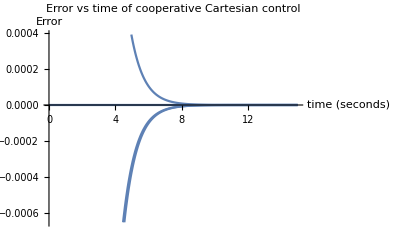

```mathematica
Plot[(z[t]/.cartmotionsim)[[13;;16]],{t, 0, 15}, AxesLabel->{"time (seconds)", "Error"}, PlotLabel->"Error vs time of cooperative Cartesian control"]
```

```mathematica
(*Visualising the motion*)
```

```mathematica
N[fkq1/.sampleα];
fin1 = fkq1/.Inner[Rule, αsym, (z[t]/.cartmotionsim/.t->0)[[7;;12]], List];
```

```mathematica
N[fkq2/.sampleβ];
fin2 =fkq2/.Inner[Rule, βsym, (z[t]/.cartmotionsim/.t->0)[[1;;6]], List];
```

```mathematica
(*Final values of tr achieved*)
```

```mathematica
dqrsf = N[dqr/.Inner[Rule, αsym, (z[t]/.cartmotionsim/.t->15)[[7;;12]], List]/.Inner[Rule, βsym, (z[t]/.cartmotionsim/.t->15)[[1;;6]], List]]
```

{{0.495628,{-0.734342,0.23616,-0.399154}},{0.135972,{0.351476,0.24312,-0.333947}}}

```mathematica
qtrsf = 2*qmult[dqrsf[[2]], cquat[dqrsf[[1]]]]
```

{-2.498×10^-16,{0.584457,-0.594277,-0.745554}}

```mathematica
trvals = Table[(z[t]/.cartmotionsim/.t->tval), {tval, 0, 15, 0.01}];
αvals = trvals[[;;, 7;;12]];
βvals = trvals[[;;, 1;;6]];
```

```mathematica
fkq1tr = fkq1/.Table[Inner[Rule, αsym, αvals[[i]], List], {i, Dimensions[αvals][[1]]}];
r1tr = Table[logdq[fkq1tr[[j]]],{j, Dimensions[αvals][[1]]}];
```

```mathematica
fkq2tr = fkq2/.Table[Inner[Rule, βsym, βvals[[i]], List], {i, Dimensions[βvals][[1]]}];
r2tr = Table[logdq[fkq2tr[[j]]],{j, Dimensions[βvals][[1]]}];
```

```mathematica
(*Translation control*)
```

```mathematica
r1tr[[-1]][[2]]-r2tr[[-1]][[2]]
```

{0.229927,0.402542,0.312642}

```mathematica
r1tr[[-1]][[2]]
```

{0.177781,0.239519,0.099364}

```mathematica
r2tr//Dimensions
```

{1501,2,3}

```mathematica
(*Snapshot trajectory*)
```

```mathematica
Dimensions[r2tr][[1]]
```

1501

### Cooperative task space Cartesian control

```mathematica
Manipulate[Show[frameplotter[2*Flatten[r1tr[[1]]]], frameplotter[2*Flatten[r1tr[[-1]]]], frameplotter[2*Flatten[r1tr[[i]]]],frameplotter[2*Flatten[r2tr[[1]]]], frameplotter[2*Flatten[r2tr[[-1]]]], frameplotter[2*Flatten[r2tr[[i]]]]],{i, 1,400 ,1}];
```

## Logarithmic dual quaternion feedback controller

```mathematica
(*Following the methodology from Bullo and Murray pg. 18 for logarithmic feedback*)
```

```mathematica
(*Which means we take the logarithmic map of SE(3) i.e. se(3) and control elements of se(3)*)
```

```mathematica
(*Find the intial relative dual quaternion and find the se(3) element corresponding to it*)
```

```mathematica
ei = dqmult[cdualq[qd2], qi];
```

```mathematica
ic = logdq[ei];
```

```mathematica
(*Now using these ase our integration initial conditions, let us integrate the differential equations*)
```

```mathematica
AMat[z_/;VectorQ[z, NumericQ]]:=Module[{ψv, ψM, Rψ, Aψ, ψ, AψIT, kw, kv, LHS},
kw =5;
kv = 5;
ψ = z[[1;;3]];
ψv = Sqrt[ψ.ψ];
ψM = vec2SkewMat[ψ];
Rψ = IdentityMatrix[3]+Sin[ψv]*ψM/ψv+(1-Cos[ψv])*ψM.ψM/ψv^2;
Aψ = IdentityMatrix[3]+(1-Cos[ψv])/ψv*ψM/ψv+(1-(Sin[ψv]/ψv))*ψM.ψM/ψv^2;
AψIT = Rψ.Inverse[Aψ];
LHS = ArrayFlatten[{{-kw*IdentityMatrix[3], ConstantArray[0, {3,3}]},{ConstantArray[0, {3,3}], -kw*IdentityMatrix[3]-kv*AψIT}}].z;
Return[LHS];
]
```

```mathematica
logerror = NDSolve[{AMat[z[t]]== z'[t], z[0]== Flatten[ic]},z, {t, 0, 15}][[1]]
```

{z→InterpolatingFunction[…]}

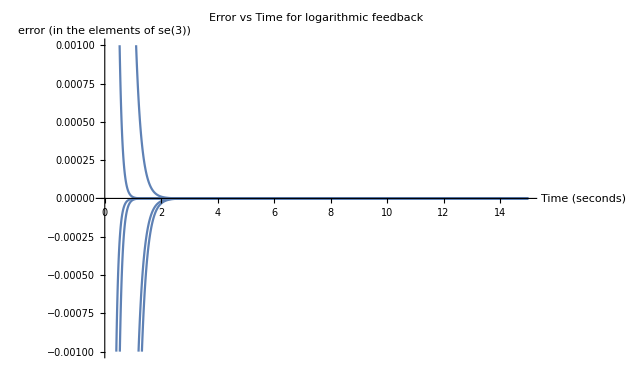

```mathematica
Plot[(z[t]/.logerror), {t, 0, 15}, PlotRange->{{0, 15}, {-0.001, 0.001}}, AxesLabel->{"Time (seconds) ", "error (in the elements of se(3))"} , PlotLabel->"Error vs Time for logarithmic feedback"]
```

```mathematica
(*This solves the regulation problem using se3*)
```

#### Verifying the properties of logarithm for dual quaternions

```mathematica
Chop[dqmult[qd2, ei]-qi]
```

{{0,{0,0,0}},{0,{0,0,0}}}

```mathematica
logdq[ei]
```

{{-0.718187,0.256739,-0.394939},{0.146114,-0.148569,-0.186389}}

```mathematica
logdq[cdualq[qd2]]+logdq[qi]
```

{{-0.918014,-0.139118,-0.159619},{0.177564,0.122519,-0.046226}}

```mathematica
(*Not the same!*)
```

```mathematica
logdq[dqmult[qd2, ei]]
```

{{-2.63132,0.470235,-0.953744},{0.0651801,0.153568,0.0241239}}

```mathematica
Chop[dqmult[qd2, explogdq[logdq[ei]]]-qi]
```

{{0,{0,0,0}},{0,{0,0,0}}}

```mathematica
config = Table[Flatten[logdq[dqmult[qd2,explogdq[R62dual[z[t]/.logerror/.t->tval]]]]],{tval, 0, 15, 0.005}];
```

```mathematica
config//Dimensions
```

{3001,6}

```mathematica
cang = Table[config[[i]][[1;;3]], {i, Dimensions[config][[1]]}];
```

```mathematica
cdist = Table[config[[i]][[4;;6]], {i, Dimensions[config][[1]]}];
```

```mathematica
(*Though interpreting these plots doesnt make sense, we can see that in the second case i.e. in config2 case, the change in the angles and the axis is very small compared to the other case*)
```

```mathematica
(*We can see from below, that if planned using the wrong controller the end-effector moves in a curved path and has some overshoot which may not be desired. Also the motion is rapid initially for the wrong control case and the controller takes huge cartesian steps per iteration*)
```

```mathematica
Show[ListPointPlot3D[2*cdist, PlotStyle->{Red}], ListPointPlot3D[zdistlow, PlotStyle->{Blue}], PlotRange->{{-0.5, 0.5}, {-0.2, 0.3}, {-0.8, 0.8}}, PlotLabel->"Path followed by the two controllers", AxesLabel->{"x", "y", "z"}]
```

-Graphics3D-

### Manipulate for low gain simulation

```mathematica
Manipulate[Show[frameplotter[config[[1]]], frameplotter[config[[-1]]], frameplotter[config[[i]]]],{i, 1, 500, 1}];
```

#### High gain simulation

```mathematica
AMat[z_/;VectorQ[z, NumericQ]]:=Module[{ψv, ψM, Rψ, Aψ, ψ, AψIT, kw, kv, LHS},
kw =185;
kv = 185;
ψ = z[[1;;3]];
ψv = Sqrt[ψ.ψ];
ψM = vec2SkewMat[ψ];
Rψ = IdentityMatrix[3]+Sin[ψv]*ψM/ψv+(1-Cos[ψv])*ψM.ψM/ψv^2;
Aψ = IdentityMatrix[3]+(1-Cos[ψv])/ψv*ψM/ψv+(1-(Sin[ψv]/ψv))*ψM.ψM/ψv^2;
AψIT = Rψ.Inverse[Aψ];
LHS = ArrayFlatten[{{-kw*IdentityMatrix[3], ConstantArray[0, {3,3}]},{ConstantArray[0, {3,3}], -kw*IdentityMatrix[3]-kv*AψIT}}].z;
Return[LHS];
]
```

```mathematica
logerrorhigh = NDSolve[{AMat[z[t]]== z'[t], z[0]== Flatten[ic]},z, {t, 0, 15}][[1]]
```

{z→InterpolatingFunction[…]}

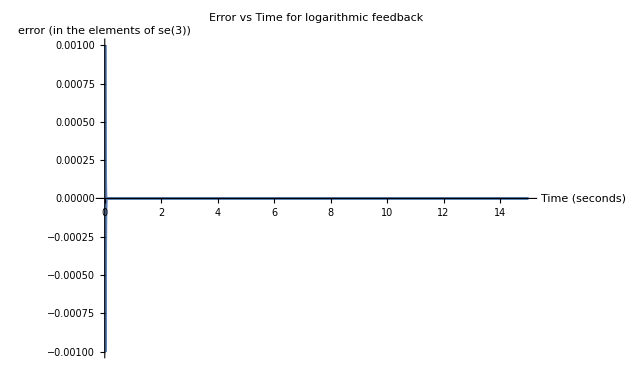

```mathematica
Plot[(z[t]/.logerrorhigh), {t, 0, 15}, PlotRange->{{0, 15}, {-0.001, 0.001}}, AxesLabel->{"Time (seconds) ", "error (in the elements of se(3))"} , PlotLabel->"Error vs Time for logarithmic feedback"]
```

```mathematica
(*This solves the regulation problem using se3*)
```

```mathematica
confighigh = Table[Flatten[logdq[dqmult[qd2,explogdq[R62dual[z[t]/.logerrorhigh/.t->tval]]]]],{tval, 0, 15, 0.001}];
```

```mathematica
confighigh//Dimensions
```

{15001,6}

```mathematica
canghigh = Table[confighigh[[i]][[1;;3]], {i, Dimensions[confighigh][[1]]}];
```

```mathematica
cdisthigh = Table[confighigh[[i]][[4;;6]], {i, Dimensions[confighigh][[1]]}];
```

```mathematica
Show[ListPointPlot3D[zdist, PlotStyle->{Blue}], ListPointPlot3D[2*cdisthigh, PlotStyle->{Red}], PlotRange->{{-0.5, 0.5}, {-0.2, 0.3}, {-0.8, 0.8}}, PlotLabel->"Path followed by the two controllers", AxesLabel->{"x", "y", "z"}]
```

-Graphics3D-

### Manipulate for high gain simulation

```mathematica
Manipulate[Show[frameplotter[confighigh[[1]]], frameplotter[confighigh[[-1]]], frameplotter[confighigh[[i]]]],{i, 1, 200, 1}];
```

### Both the low gain simulations together

```mathematica
Manipulate[Show[frameplotter[Flatten[zloglow[[1]]]], frameplotter[Flatten[zloglow[[500]]]], frameplotter[Flatten[zloglow[[i]]]],frameplotter[2*config[[1]]], frameplotter[2*config[[500]]], frameplotter[2*config[[i]]]],{i, 1, 500, 1}];
```

### Both the high gain simulations together

```mathematica
Manipulate[Show[frameplotter[Flatten[zlog[[1]]]], frameplotter[Flatten[zlog[[-1]]]], frameplotter[Flatten[zlog[[i]]]], frameplotter[2*confighigh[[1]]], frameplotter[2*confighigh[[-1]]], frameplotter[2*confighigh[[i]]]],{i, 1, 300, 1}];
```

### Manipulation trying to show the trajectory and the path in one plot, using frames for time histories Comparison of both w.r.t. error and gains

```mathematica
(*Config - logc, zang - diffc*)
```

```mathematica
Manipulate[Show[frameplotter[Flatten[zloglow[[-1]]]], Table[frameplotter[Flatten[zloglow[[i]]]], {i, j}]],{j, 1, 600, 1}]
```

```mathematica
(*Below is manipulate for high gain, i.e. for same error reduction, it requires higher gain*)
```

```mathematica
Manipulate[Show[frameplotter[Flatten[zlog[[-1]]]], Table[frameplotter[Flatten[zlog[[i]]]], {i, j}]],{j, 1, 100, 1}]
```

```mathematica
Manipulate[Show[frameplotter[2*config[[-1]]], Table[frameplotter[2*config[[i]]], {i, j}]],{j, 1, 600, 1}]
```

```mathematica
(*The above manipulate shows the trajectory for low gains of both the controllers*)
```

Important characteristic is how the diffc has a curvature in the motion whereas logc has smaller curvature.
And how low gains are sufficient in logarithmic control almost 100 times lesser.
How the exponential controller is aggressive in the starting and slowly approaches to the desired. Also high gains make both the controllers aggressive.
Logarithmic controller is faster in reaching the desired state.